```mathematica
outputdir="/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/";
```

{{:0,:1,:2},{3.,0,0},{2.9,0,0},{2.8,0,0},{2.7,0,0},{2.6,0,0},{2.5,0,0},{2.4,0,0},{2.3,0,0},{2.2,0,0},{2.1,0,0},{2.,0,0},{1.9,0,0},{1.8,0,0},{1.7,0,0},{1.6,0,0},{1.5,0,0},{1.4,0,0},{1.3,0,0},{1.2,0,0},{1.1,0,0},{1.,0,0}}

{{3.,0,0},{2.9,0,0},{2.8,0,0},{2.7,0,0},{2.6,0,0},{2.5,0,0},{2.4,0,0},{2.3,0,0},{2.2,0,0},{2.1,0,0},{2.,0,0},{1.9,0,0},{1.8,0,0},{1.7,0,0},{1.6,0,0},{1.5,0,0},{1.4,0,0},{1.3,0,0},{1.2,0,0},{1.1,0,0},{1.,0,0}}

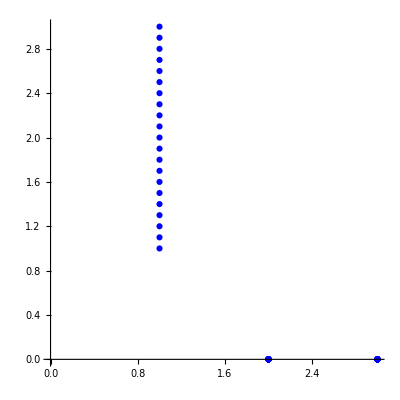

21

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/1d/line/solution/vertices.csv"]
tabve=Table[tabve[[i]],{i,2,Length[tabve]}]
ListPlot[tabve,PlotStyle->Blue,AspectRatio->1]
Length[tabve]
```

```mathematica
(*write v from ODE to csv file*)
```

```mathematica
tabv=Table[Flatten[{{v[x],0,0}/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]}],{i,1,Length[tabve]}];
PrependTo[tabv,{"f:0","f:1","f:2",":0",":1",":2"}]
```

```mathematica
Export[outputdir<>"v.csv",tabv]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/v.csv

```mathematica
(*write w from ODE to csv file*)
```

```mathematica
tabw=Table[{w[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabw,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{0,3.,0,0},{0,2.9,0,0},{0,2.8,0,0},{0,2.7,0,0},{0,2.6,0,0},{0,2.5,0,0},{0,2.4,0,0},{0,2.3,0,0},{0,2.2,0,0},{0,2.1,0,0},{0,2.,0,0},{0,1.9,0,0},{0,1.8,0,0},{0,1.7,0,0},{0,1.6,0,0},{0,1.5,0,0},{0,1.4,0,0},{0,1.3,0,0},{0,1.2,0,0},{0,1.1,0,0},{0,1.,0,0}}

```mathematica
Export[outputdir<>"w.csv",tabw]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/w.csv

```mathematica
(*write σ from ODE to csv file*)
```

```mathematica
tabσ=Table[{σ[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabσ,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{0,3.,0,0},{0,2.9,0,0},{0,2.8,0,0},{0,2.7,0,0},{0,2.6,0,0},{0,2.5,0,0},{0,2.4,0,0},{0,2.3,0,0},{0,2.2,0,0},{0,2.1,0,0},{0,2.,0,0},{0,1.9,0,0},{0,1.8,0,0},{0,1.7,0,0},{0,1.6,0,0},{0,1.5,0,0},{0,1.4,0,0},{0,1.3,0,0},{0,1.2,0,0},{0,1.1,0,0},{0,1.,0,0}}

```mathematica
Export[outputdir<>"sigma.csv",tabσ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/sigma.csv

```mathematica
(*write ψ from ODE to csv file*)
```

```mathematica
tabψ=Table[{ψ[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabψ,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{2.,3.,0,0},{1.97028,2.9,0,0},{1.90239,2.8,0,0},{1.79721,2.7,0,0},{1.65642,2.6,0,0},{1.48287,2.5,0,0},{1.28095,2.4,0,0},{1.05682,2.3,0,0},{0.818314,2.2,0,0},{0.57454,2.1,0,0},{0.335099,2.,0,0},{0.109185,1.9,0,0},{-0.0952085,1.8,0,0},{-0.27176,1.7,0,0},{-0.415913,1.6,0,0},{-0.524676,1.5,0,0},{-0.596269,1.4,0,0},{-0.629755,1.3,0,0},{-0.624763,1.2,0,0},{-0.581345,1.1,0,0},{-0.5,1.,0,0}}

```mathematica
Export[outputdir<>"psi.csv",tabψ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/psi.csv

```mathematica
(*write μ from ODE to csv file*)
```

```mathematica
tabμ=Table[{H[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabμ,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{-0.0524743,3.,0,0},{-0.244488,2.9,0,0},{-0.433678,2.8,0,0},{-0.616761,2.7,0,0},{-0.788819,2.6,0,0},{-0.94303,2.5,0,0},{-1.07099,2.4,0,0},{-1.16376,2.3,0,0},{-1.21365,2.2,0,0},{-1.21602,2.1,0,0},{-1.17066,2.,0,0},{-1.08178,1.9,0,0},{-0.956883,1.8,0,0},{-0.804854,1.7,0,0},{-0.634214,1.6,0,0},{-0.451965,1.5,0,0},{-0.263205,1.4,0,0},{-0.0713574,1.3,0,0},{0.121237,1.2,0,0},{0.31254,1.1,0,0},{0.5,1.,0,0}}

```mathematica
Export[outputdir<>"mu.csv",tabμ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/mu.csv

```mathematica
(*write X from ODE to csv file*)
```

```mathematica
tabX=Table[Flatten[{{X1[x],X2[x],0}/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]}],{i,1,Length[tabve]}];
PrependTo[tabX,{"f:0","f:1","f:2",":0",":1",":2"}]
```

```mathematica
Export[outputdir<>"X.csv",tabX]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/X.csv